```mathematica
F1=B*Sin[ϕ]+A*Cos[ϕ]*ϕ1-A*ω*Cos[ϕ]
```

A ϕ1 Cos[ϕ]-A ω Cos[ϕ]+B Sin[ϕ]

```mathematica
FullSimplify[F1-B*Sin[ϕ]]
```

A (ϕ1-ω) Cos[ϕ]

```mathematica
F2=m*(B*ω*Cos[ϕ]-A*ω*Sin[ϕ]*ϕ1)+b*A*ω*Cos[ϕ]+c*A*Sin[ϕ]-a1*V*A*ω*Cos[ϕ]+a3/V^3*A^3ω^3*Cos[ϕ]^3
```

A b ω Cos[ϕ]-A a1 V ω Cos[ϕ]+(A^3 a3 ω^3 Cos[ϕ]^3)/V^3+A c Sin[ϕ]+m (B ω Cos[ϕ]-A ϕ1 ω Sin[ϕ])

```mathematica
FullSimplify[m*Cos[ϕ]*ω*F1-F2*Sin[ϕ]]
```

A (m (ϕ1-ω) ω Cos[ϕ]^2+(-b+a1 V) ω Cos[ϕ] Sin[ϕ]-(A^2 a3 ω^3 Cos[ϕ]^3 Sin[ϕ])/V^3+(-c+m ϕ1 ω) Sin[ϕ]^2)

```mathematica
Integrate[Cos[a]^4,{a,0,2π}]
```

(3 π)/4

```mathematica
Integrate[1/(A/2-3*A^3*ω^2/8),A]
```

8 (Log[A]/4-1/8 Log[-4+3 A^2 ω^2])

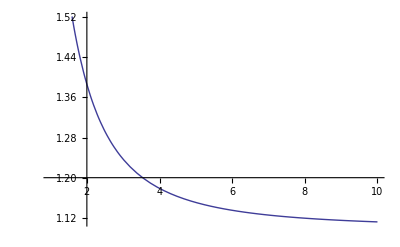

```mathematica
Plot[-8 (Log[A]/4-1/8 Log[4+3 A^2]),{A,1,10}]
```